# Задание № 9.

## Методы Монте-Карло

## Кладов Сергей Алексеевич, 20373

## Задание

Все задачи в этом задании взяты из методического пособия Войтишек А.В. Символьные и численные расчеты в физических приложениях. Вам нужно выполнить (воспроизвести) математические выкладки с помощью системы Wolfram Mathematica, реализовать генераторы, построить гистограммы и плотности распределения.

### Метод обратной функции распределения. Конструирование моделируемых плотностей

При численном решении задач теории переноса излучения широко используется индикатриса Хеньи-Гринстейна, представляющая собой плотность распределения косинуса угла рассеяния  u при столкновении “фотона” с частицей среды cледующего вида

f(u)=(1-μ^2)/(2(1+μ^2-2μ u)^(3/2)), u∈(-1,+1)

Плотность распределения зависит от параметра  μ∈(-1,1). Постройте метод генерации u в соответствии с эти распределением, постройте гистограммы + графики  плотностей распределения при разных μ (графики могут быть интерактивными).

```mathematica
clear[distr,genF];
distr[μ_]:=ProbabilityDistribution[0.5(1-μ^2)/(1+μ^2-2μ u)^1.5,{u,-1,1}];
genF[μ_]:=InverseCDF[distr[μ],RandomReal[]];
```

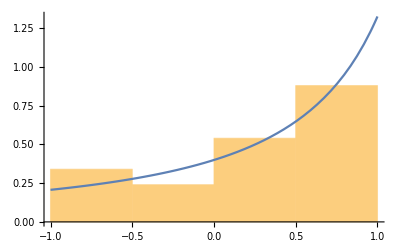

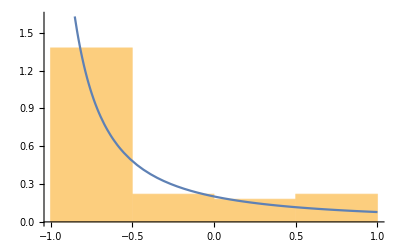

```mathematica
Show[{Histogram[Table[genF[0.3],{100}],Automatic,PDF],Plot[PDF[distr[0.3]][x],{x,-1,1}]}]
Show[{Histogram[Table[genF[-0.6],{100}],Automatic,PDF],Plot[PDF[distr[-0.6]][x],{x,-1,1}]}]
```

### Конструирование двумерного моделируемого вектора с зависимыми координатами

Сформулируйте стандартный метод моделирования случайного вектора и продемонстрируйте его на примере двумерного вектора (ξ, η), имеющего плотность распределения. Постройте 2-мерные гистограмму + плотность распределения.

f(u,v)=3 u^2(u+1)v^u e^(-u^3),  0<u<∞, 0<v<1

```mathematica
Integrate[3 u^2(u+1)v^u e^(-u^3),{v,0,1},Assumptions->{u>0}]
```

3 e^(-u^3) u^2

```mathematica
clear[distr,genU,distr1,genV,u];
distr:=ProbabilityDistribution[3Exp[-u^3]u^2,{u,0,∞}];
genU:=InverseCDF[distr,RandomReal[]];
distr1[u_]:=ProbabilityDistribution[(u+1)v^u,{v,0,1}];
genV[u_]:=InverseCDF[distr1[u],RandomReal[]];
```

```mathematica
hist=Histogram3D[Table[With[{u=genU},{genV[u],u}],{100}],Automatic,PDF]
plot=Plot3D[3u^2(u+1)v^u Exp[-u^3],{v,0,1},{u,0,3}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[{hist,plot}]
```

-Graphics3D-

### Метод дискретной суперпозиции

Требуется построить алгоритм моделирования случайной величины ξ, имеющей плотность распределения.

f(u)=(5u)/((1+u^2)^2)+(√2 π)/(8 u^2)sin(π/(2u)), 1<u<2

```mathematica
clear[distr,distr1,distr2,genF];
p1=Integrate[5u/(1+u^2)^2,{u,1,2}];
p2=Integrate[Sqrt[2]π Sin[π/(2u)]/(8 u^2),{u,1,2}];
distr:=ProbabilityDistribution[(5u/(1+u^2)^2/p1+Sqrt[2]π Sin[π/(2u)]/(8 u^2))/(p1+p2),{u,1,2}];
distr1:=ProbabilityDistribution[5u/(1+u^2)^2/p1,{u,1,2}];
distr2:=ProbabilityDistribution[Sqrt[2]π Sin[π/(2u)]/(8 u^2)/p2,{u,1,2}];
genF:=With[{r=RandomReal[]},If[r<p1,InverseCDF[distr1,r],InverseCDF[distr2,r]]];
```

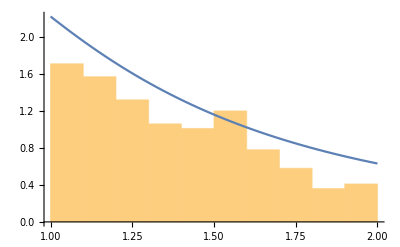

```mathematica
Show[{Histogram[Table[genF,{1000}],Automatic,PDF],Plot[PDF[distr][x],{x,1,2}]}]
```

### Метод исключения

Рассмотрим случайную величину ξ, имеющую плотность распределения (здесь lg - десятичный логарифм)

f(u)=1/(Ḡ(u^2 lg(u+10)+10)), 0 < u <1

Нормировка плотности распределения в элементарных функциях не вычисляется

Ḡ=(∫_0)^1 ⅆu/(u^2 lg(u+10)+10)

Реализуйте алгоритм метода исключения для этой случайной величины.

Как только у вас будет генератор вы можете оценить интеграл Ḡ методом Монте-Карло (как?). Оцените погрешность оценки Ḡ методом Монте-Карло. Как ведет себя погрешность с увеличением n числа разыгранных случайных величин (попробуйте n = 10, 100, 1000, 10000).

Сравните со значением Ḡ, которое дает NIntegrate.

Постройте гистограмму и плотность распределения.

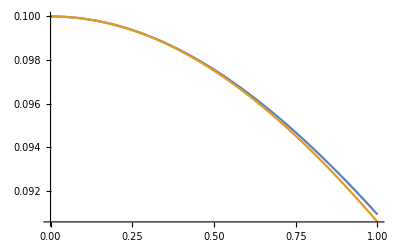

```mathematica
Plot[{1/(u^2+10),1/(u^2Log10[u+10]+10)},{u,0,1}]
```

```mathematica
clear[distrM,genM,genF];
f[ξ_]:=1/(ξ^2Log10[ξ+10]+10)
pM=Integrate[1/(u^2+10),{u,0,1}];
distrM:=ProbabilityDistribution[(1/pM)/(u^2+10),{u,0,1}];
genM:=InverseCDF[distrM,RandomReal[]];
genF:=(
ξ0=genM;
η0=RandomReal[]/(ξ0^2+10);
While[η0>f[ξ0],{ξ0=genM,0=RandomReal[]/(ξ0^2+10)}];
ξ0
)
```

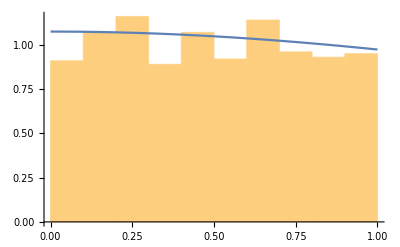

```mathematica
G=NIntegrate[1/(u^2Log[u+10]+10),{u,0,1}];
Show[{Histogram[Table[genF,{1000}],Automatic,PDF],Plot[f[x]/G,{x,0,1}]}]
```

```mathematica
int[n_]:=Total[Table[f[genF],{n}]]/n
int[100]
G
```

0.0966633

0.0930556

### Выборка по важности

Реализуйте алгоритм выборки по важности для вычисления 4-кратного интеграла. Оцените дисперсию вычислений (точек потребуется достаточно много). Попробуйте сравнить с NIntegrate  (с разными стратегиями интегрирования и опциями вычислений)

I=1/(2π)^2(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)(∫_(-∞))^(+∞)ⅇ^(-(x_1^2+x_2^2+x_3^2+x_4^2)/2)√(1+(sin^3(x_1 x_2 x_3 x_4))/12)ⅆ x_1ⅆ x_2ⅆ x_3ⅆ x_4

```mathematica
genξ:=InverseCDF[NormalDistribution[0,1],RandomReal[]];
int[n_]:=Total[Table[With[{ξ1=genξ,ξ2=genξ,ξ3=genξ,ξ4=genξ},Sqrt[1+(Sin[ξ1 ξ2 ξ3 ξ4])^3/12]],{n}]]/n
```

```mathematica
int[10000]
NIntegrate[Exp[-(ξ1^2+ξ2^2+ξ3^2+ξ4^2)/2]Sqrt[1+(Sin[ξ1 ξ2 ξ3 ξ4])^3/12],{ξ1,-∞,∞},{ξ2,-∞,∞},{ξ3,-∞,∞},{ξ4,-∞,∞}]/(2π)^2
NIntegrate[Exp[-(ξ1^2+ξ2^2+ξ3^2+ξ4^2)/2]Sqrt[1+(Sin[ξ1 ξ2 ξ3 ξ4])^3/12],{ξ1,-∞,∞},{ξ2,-∞,∞},{ξ3,-∞,∞},{ξ4,-∞,∞},Method->"GlobalAdaptive"]/(2π)^2
NIntegrate[Exp[-(ξ1^2+ξ2^2+ξ3^2+ξ4^2)/2]Sqrt[1+(Sin[ξ1 ξ2 ξ3 ξ4])^3/12],{ξ1,-∞,∞},{ξ2,-∞,∞},{ξ3,-∞,∞},{ξ4,-∞,∞},Method->"MonteCarlo"]/(2π)^2
```

0.999775

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4764 and 0.00712146 for the integral and error estimates.

0.999948

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4764 and 0.00712146 for the integral and error estimates.

0.999948

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 39.8286 and 1.08184 for the integral and error estimates.

1.00887

```mathematica
disp[n_]:=With[{l=Table[With[{ξ1=genξ,ξ2=genξ,ξ3=genξ,ξ4=genξ},Sqrt[1+(Sin[ξ1 ξ2 ξ3 ξ4])^3/12]],{n}]},(Total[l^2]-Total[l]^2/n)/(n-1)]
```

```mathematica
disp[100000]
```

0.000114743